```mathematica
(* This file looks at the radial distribution function for the same simulation as I did in Smoldyn but with SpringSaLaD. *)
```

```mathematica
SetDirectory["~/SSA/INI/Smoldyn/SpringSaLaD"]
```

/Users/sandrews/SSA/INI/Smoldyn/SpringSaLaD

```mathematica
maxradius=20
nmolec=6112
volume=1000000
radius=2.5
```

20

6112

1000000

2.5

```mathematica
(* Everything below here should take care of itself *)
```

```mathematica
(* Define functions *)
```

```mathematica
changfunction[h_,x_]:=Module[{Avalue,Bvalue,Cvalue,zd,zs,yplus,yminus,f,a1,a2,a3,b1,b2,b3,b4,b5,b6,c1,c2,c3,c4,c5,c6,c7,c8,c9,H1,H2,H3,g},
Avalue=(-2*h+zd)/(1-h);
Bvalue=(-2h-zd/2)/(1-h);
Cvalue=Sqrt[3]*zs/(2*(1-h));
zd=yplus-yminus;
zs=yplus+yminus;
yplus=(2*h*f)^(1/3)*(Sqrt[2*h^4/f^2+1]+1)^(1/3);
yminus=(2*h*f)^(1/3)*(Sqrt[2*h^4/f^2+1]-1)^(1/3);
f=3+3*h-h^2;
a1=(-2*h*(1-h-3*h^2)+(1-3*h-4*h^2)*zd+(1+h/2)*zd^2)/(3*(2*h^2+zd^2)*(1-h)^2);
a2=(h*(2+4*h-3*h^2)-(1-3*h-4*h^2)*zd+2*(1+h/2)*zd^2)/(3*(2*h^2+zd^2)*(1-h)^2);
a3=((1-3*h-4*h^2)*(4*h^2+zd^2)+h*(2-5*h^2)*zd)/(Sqrt[3]*zs*(2*h^2+zd^2)*(1-h)^2);
b1=-4/3*h*((2*h^2-zd^2)*(1-6*h-3*h^2+20*h^3+15*h^4)+zd*h*(16+24*h-21*h^2-13*h^3+21*h^4))/((2*h^2+zd^2)^3*(1-h)^2);
b2=-b1;
b3=8*Sqrt[3]*h^2*((4*h^2+zd^2)*(2-10*h-24*h^2+30*h^3+79*h^4+21*h^5-17*h^6)+2*zd*h*(16+40*h-h^2-50*h^3+11*h^4+52*h^5+13*h^6))/(zs^3*(2*h^2+zd^2)^3*(1-h)^2);
b4=-2/3*h*(2*h*(10+28*h+21*h^2-13*h^3-19*h^4)+zd*(2-12*h-18*h^2+28*h^3+27*h^4)+zd^2*(4-6*h-18*h^2-7*h^3))/((2*h^2+zd^2)^2*(1-h)^3);
b5=-4/3*h^2*(4*(6-30*h-82*h^2+58*h^3+222*h^4+94*h^5-25*h^6)-zd*(24-10*h-164*h^2-156*h^3+22*h^4+41*h^5)-zd^2*(10+32*h+15*h^2-31*h^3-26*h^4))/(zs^2*(2*h^2+zd^2)^2*(1-h)^3);
b6=4/Sqrt[3]*h^2*(24-10*h-164*h^2-156*h^3+22*h^4+41*h^5-zd*(10+32*h+15*h^2-31*h^3-26*h^4))/(zs*(2*h^2+zd^2)^2*(1-h)^3);
c1=-32*h^3*((2*h^2-zd^2)*(4-56*h-136*h^2+130*h^3+343*h^4-268*h^5-665*h^6-170*h^7+89*h^8)+zd*h*(92+116*h-744*h^2-1468*h^3+332*h^4+1902*h^5+251*h^6-925*h^7-285*h^8))/(zs^2*(2*h^2+zd^2)^5*(1-h)^2);
c2=-c1;
c3=64*Sqrt[3]*h^4*((4*h^2+zd^2)*(24-312*h-1252*h^2-40*h^3+3854*h^4+1658*h^5-6616*h^6-6376*h^7+593*h^8+1799*h^9+107*h^10)+2*zd*h*(276+624*h-1960*h^2-6976*h^3-3208*h^4+8690*h^5+7499*h^6-4996*h^7-6541*h^8-610*h^9+641*h^10))/(zs^5*(2*h^2+zd^2)^5*(1-h)^2);
c4=-8/3*h^2*(2*h*(36-92*h-360*h^2+156*h^3+982*h^4+747*h^5+195*h^6+37*h^7)-3*zd*h*(4+8*h-94*h^2-60*h^3+280*h^4+256*h^5+11*h^6)+zd^2*(4-60*h-84*h^2+190*h^3+150*h^4-258*h^5-185*h^6))/((2*h^2+zd^2)^4*(1-h)^3);
c5=-32*h^4*(96-1248*h-4960*h^2-256*h^3+14976*h^4+7232*h^5-24376*h^6-25632*h^7-724*h^8+5348*h^9+384*h^10-zd*(72-96*h-1152*h^2-932*h^3+3012*h^4+4920*h^5+604*h^6-2286*h^7-708*h^8+211*h^9)+zd^2*(12-24*h-110*h^2+150*h^3+522*h^4-32*h^5-774*h^6-462*h^7-11*h^8))/(zs^4*(2*h^2+zd^2)^4*(1-h)^3);
c6=32*Sqrt[3]*h^4*(72-96*h-1152*h^2-932*h^3+3012*h^4+4920*h^5+604*h^6-2286*h^7-708*h^8+211*h^9+zd*(12-24*h-110*h^2+150*h^3+522*h^4-32*h^5-774*h^6-462*h^7-11*h^8))/(zs^3*(2*h^2+zd^2)^4*(1-h)^3);
c7=2/3*h^2*(4*h*(34+18*h-195*h^2-332*h^3-144*h^4+69*h^5+64*h^6)+2*zd*(2+6*h+30*h^2+176*h^3+174*h^4-66*h^5-79*h^6)+3*zd^2*(4-14*h-32*h^2+32*h^3+68*h^4+23*h^5))/((2*h^2+zd^2)^3*(1-h)^4);
c8=-8/3*h^3*(12+48*h+280*h^2+1224*h^3+1776*h^4-80*h^5-1794*h^6-816*h^7+79*h^8+zd*(36-88*h-420*h^2+72*h^3+1172*h^4+897*h^5-63*h^6-148*h^7)-zd^2*(68+48*h-432*h^2-760*h^3-192*h^4+342*h^5+197*h^6))/(zs^2*(2*h^2+zd^2)^3*(1-h)^4);
c9=8/3*Sqrt[3]*h^3*((4*h^2+zd^2)*(36-88*h-420*h^2+72*h^3+1172*h^4+897*h^5-63*h^6-148*h^7)-zd*(12+48*h+416*h^2+1320*h^3+912*h^4-1600*h^5-2178*h^6-132*h^7+473*h^8))/(zs^3*(2*h^2+zd^2)^3*(1-h)^4);
H1=a1*Exp[Avalue*(x-1)]+a2*Exp[Bvalue*(x-1)]*Cos[Cvalue*(x-1)]+a3*Exp[Bvalue*(x-1)]*Sin[Cvalue*(x-1)];
H2=b1*Exp[Avalue*(x-2)]+
b2*Exp[Bvalue*(x-2)]*Cos[Cvalue*(x-2)]+
b3*Exp[Bvalue*(x-2)]*Sin[Cvalue*(x-2)]+
b4*(x-2)*Exp[Avalue*(x-2)]+
b5*(x-2)*Exp[Bvalue*(x-2)]*Cos[Cvalue*(x-2)]+b6*(x-2)*Exp[Bvalue*(x-2)]*Sin[Cvalue*(x-2)];
H3=c1*Exp[Avalue*(x-3)]+
c2*Exp[Bvalue*(x-3)]*Cos[Cvalue*(x-3)]+
c3*Exp[Bvalue*(x-3)]*Sin[Cvalue*(x-3)]+
c4*(x-3)*Exp[Avalue*(x-3)]+
c5*(x-3)*Exp[Bvalue*(x-3)]*Cos[Cvalue*(x-3)]+
c6*(x-3)*Exp[Bvalue*(x-3)]*Sin[Cvalue*(x-3)]+
c7*(x-3)^2*Exp[Avalue*(x-3)]+
c8*(x-3)^2*Exp[Bvalue*(x-3)]*Cos[Cvalue*(x-3)]+
c9*(x-3)^2*Exp[Bvalue*(x-3)]*Sin[Cvalue*(x-3)];
g=1/x*(HeavisideTheta[x-1]*H1+HeavisideTheta[x-2]*H2+HeavisideTheta[x-3]*H3);
g]
```

```mathematica
(* Load and look at data *)
```

```mathematica
simdata=Import["resultsSSLD.csv","CSV"];
```

```mathematica
simdata1=Transpose[Drop[Transpose[simdata],4]];
```

```mathematica
simdata1[[1;;10]]
```

{{21.2533,-28.4807,40.3847},{14.5512,7.43294,53.5862},{-17.3444,-37.5892,70.0226},{-24.6111,43.8639,30.0849},{-24.0894,12.1994,80.4953},{-28.9737,-1.22477,71.4022},{13.8983,4.82612,76.7422},{-22.2894,24.0803,48.5},{25.216,-26.3747,36.7806},{35.9252,33.8763,26.5237}}

```mathematica
{Min[simdata1[[All,1]]],Max[simdata1[[All,1]]]}
{Min[simdata1[[All,2]]],Max[simdata1[[All,2]]]}
{Min[simdata1[[All,3]]],Max[simdata1[[All,3]]]}
```

{-47.4968,47.4955}

{-47.4961,47.4947}

{2.50222,97.4999}

```mathematica
(* Computes the radial distribution function about a single point *)
rdfpt[x_,data_,distmax_,bins_]:=Last[Last[Module[{bin,dist,hist,i},
hist=Table[0,{bins}];
For[i=1,i<=Length[data],i++,{
dist=Sqrt[(data[[i,1]]-x[[1]])^2+(data[[i,2]]-x[[2]])^2+(data[[i,3]]-x[[3]])^2];
bin=Floor[dist*bins/distmax];
If[bin>0&&bin≤bins,hist[[bin]]++]}]
Return[hist]]]]
```

```mathematica
ans=rdfpt[{0,0,50},simdata1,10,10]
```

{1,0,0,3,2,5,1,6,11,10}

```mathematica
nbin=100
```

100

```mathematica
hist=Table[0,{nbin}];
For[i=1,i≤Length[simdata1],i++,{
x=simdata1[[i]];
If[x[[1]]>-30&&x[[1]]<30&&x[[2]]>-30&&x[[2]]<30&&x[[3]]>20&&x[[3]]<80,hist+=rdfpt[x,simdata1,maxradius,nbin]]}]
```

```mathematica
hist
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,776,2050,1573,1390,1307,1177,1127,1012,1023,966,896,903,954,922,1044,1103,1145,1243,1391,1444,1586,1822,2043,2223,2372,2521,2715,2802,2837,2940,2899,2932,3027,3221,3046,3118,3067,3247,3201,3438,3579,3721,3811,3980,4387,4489,4630,4674,4834,5126,5191,5456,5334,5749,5721,6076,6053,6093,6033,6173,6311,6457,6623,6924,6962,7305,7474,7551,7648,7924,8256,8439,8630,8963,8888,9317,9133}

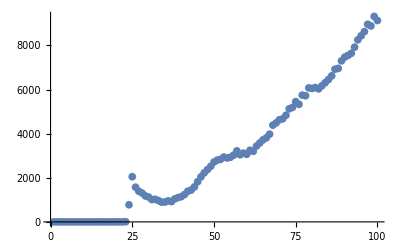

```mathematica
ListPlot[hist]
```

```mathematica
binwidth=N[maxradius/nbin]
```

0.2

```mathematica
xvector=Table[i,{i,binwidth*3/2,maxradius+binwidth/2,binwidth}]
```

{0.3,0.5,0.7,0.9,1.1,1.3,1.5,1.7,1.9,2.1,2.3,2.5,2.7,2.9,3.1,3.3,3.5,3.7,3.9,4.1,4.3,4.5,4.7,4.9,5.1,5.3,5.5,5.7,5.9,6.1,6.3,6.5,6.7,6.9,7.1,7.3,7.5,7.7,7.9,8.1,8.3,8.5,8.7,8.9,9.1,9.3,9.5,9.7,9.9,10.1,10.3,10.5,10.7,10.9,11.1,11.3,11.5,11.7,11.9,12.1,12.3,12.5,12.7,12.9,13.1,13.3,13.5,13.7,13.9,14.1,14.3,14.5,14.7,14.9,15.1,15.3,15.5,15.7,15.9,16.1,16.3,16.5,16.7,16.9,17.1,17.3,17.5,17.7,17.9,18.1,18.3,18.5,18.7,18.9,19.1,19.3,19.5,19.7,19.9,20.1}

```mathematica
Length[xvector]
```

100

```mathematica
rdf=Table[N[hist[[i]]/(i^3-(i-1)^3)],{i,1,Length[hist]}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00394997,0.468316,1.13826,0.806253,0.659706,0.576025,0.482971,0.431635,0.362594,0.343635,0.304828,0.266112,0.25287,0.252314,0.230673,0.247452,0.248032,0.244606,0.252591,0.269208,0.26647,0.279373,0.306682,0.328933,0.342685,0.350421,0.357234,0.369338,0.366227,0.356541,0.355545,0.337603,0.329032,0.327562,0.336327,0.307087,0.303691,0.288768,0.295693,0.282101,0.29337,0.295858,0.298133,0.296092,0.299992,0.320945,0.318889,0.319509,0.31346,0.315185,0.325068,0.320294,0.327668,0.311912,0.327448,0.317498,0.328663,0.319234,0.31341,0.302755,0.302316,0.301716,0.301433,0.301993,0.30846,0.303104,0.310891,0.311015,0.307313,0.304495,0.308699,0.31479,0.314994,0.315412,0.320829,0.311652,0.320095,0.307498}

```mathematica
rdf=rdf/rdf[[-1]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0128455,1.52299,3.70167,2.62198,2.1454,1.87326,1.57065,1.4037,1.17918,1.11752,0.991317,0.865411,0.822348,0.820539,0.750161,0.804727,0.806614,0.795471,0.821439,0.87548,0.866574,0.908536,0.997347,1.06971,1.11443,1.13959,1.16174,1.20111,1.19099,1.15949,1.15625,1.0979,1.07003,1.06525,1.09375,0.998665,0.987621,0.939087,0.961608,0.917407,0.954054,0.962147,0.969545,0.962907,0.975591,1.04373,1.03704,1.03906,1.01939,1.025,1.05714,1.04161,1.06559,1.01435,1.06488,1.03252,1.06883,1.03817,1.01923,0.984575,0.983149,0.981197,0.980277,0.982096,1.00313,0.985711,1.01103,1.01144,0.9994,0.990234,1.00391,1.02371,1.02438,1.02574,1.04335,1.01351,1.04097,1.}

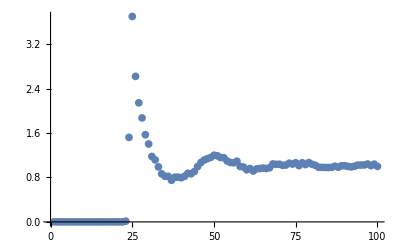

```mathematica
ListPlot[rdf]
```

```mathematica
rdfxy=Transpose[{xvector,rdf}];
```

```mathematica
h=0.4
```

0.4

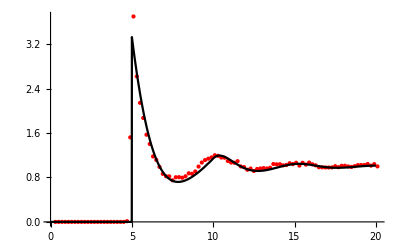

```mathematica
Show[{ListPlot[rdfxy,PlotStyle->Directive[Red,PointSize[Medium]]],Plot[changfunction[h,x/(2*radius)],{x,0,4*(2*radius)},PlotStyle->Black,Exclusions->None]},PlotRange->All,AxesStyle->Directive[Bold,12]]
```